```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[] <> "\\Code\\Output"];
```

# Визуализация численного решения линейного одномерного уравнения переноса

## Получение аналитического решения

```mathematica
(* Объявление задачи *)
eq = D[u[x, t], t] + a D[u[x, t], x] == 0;
a = 1;
l1 = -1;
l2 = 1;
u0[x_]=  (x-l1)/(l2-l1);
(*u0[x_]=  1;*)
ic = u[x, 0] == u0[x];
(* Аналитическое решение *)
sol = DSolve[{eq, ic}, u[x, t], {x, t}][[1]][[1]][[2]]
(* Численное решение Wolfram'a *)
(*nsol = NDSolve[{eq, ic}, u[x, t], {x, -1, 1}, {t, 0, 1}][[1]][[1]][[2]]*)
```

1/2 (1-t+x)

```mathematica
Manipulate[Plot[Evaluate[sol/.{x->coord, t->time}], {coord, l1, l2}], {time, 0, 1}]
```

Plot::plln: Limiting value l1 in {coord,l1,l2} is not a machine-sized real number.

## Модуль для визуализации численного решения

```mathematica
(* Модуль возвращающий индекс первого элемента table, который больше заданного числа*)
FindIndex[table_, num_]:=Module[{index},index=FirstPosition[table,_?(#>num&)];
If[index===Missing["NotFound"],Missing["NotFound"],index[[1]]]]
```

```mathematica
LTEPlotDATA[data_, sol_,  ifjoin_: False]:= Module[{plotdata},
coord1 = FindIndex[data[[1]][[2;;]], -1];
coord2 = FindIndex[data[[1]][[2;;]], 1];

plotdata = Manipulate[ListPlot[Table[{data[[1]][[coord]],data[[time]][[coord]]},{coord, coord1,coord2, 1}
], Joined->ifjoin, PlotRange->{{-1, 1},{-1, 1}}, AxesLabel->{"x", "u(x, t)"},
   PlotStyle -> Black, ImageSize->{400,400},LabelStyle->{FontSize->15},
AspectRatio->1, Frame->True,AxesOrigin->{0,0}, GridLines->Automatic, PlotLabel->"Численное"],
{time, 2,Length@data, 1}];
plotdata
]



LTEPlotSOL[data_, sol_,  ifjoin_: False]:= Module[{plotsol, coord1, coord2},

coord1 = FindIndex[data[[1]][[2;;]], -1];
coord2 = FindIndex[data[[1]][[2;;]], 1];

plotsol = Manipulate[ListPlot[Table[{data[[1]][[coord]], Evaluate[sol /. {t-> data[[time]][[1]], x -> data[[1]][[coord]]}]}, {coord, coord1,coord2, 1}
], Joined->ifjoin, PlotRange->{{-1, 1},{-1, 1}}, AxesLabel->{"x", "u(x, t)"},   PlotStyle -> Black, ImageSize->{400,400},LabelStyle->{FontSize->15},AspectRatio->1, Frame->True,AxesOrigin->{0,0}, GridLines->Automatic , PlotLabel->"Точное"],{time, 2,Length@data, 1}];



plotsol
]


LTEPlotERR[data_, sol_,  ifjoin_: False]:= Module[{ploterr,coord1, coord2},
coord1 = FindIndex[data[[1]][[2;;]], -1];
coord2 = FindIndex[data[[1]][[2;;]], 1];


ploterr = ListPlot[
Table[{data[[time]][[1]],
Max[Table[Abs[data[[time]][[coord]] - Evaluate[sol/.{x->data[[1]][[coord]], t-> data[[time]][[1]]}]], {coord, coord1,coord2, 1}]]},

 {time, 2,Length@data, 1}],
Joined->False, PlotRange->{{0, data[[-1]][[1]]},Automatic}, AxesLabel->{"time", "ERR"},PlotStyle -> Black, ImageSize->{400,400},LabelStyle->{FontSize->15},AspectRatio->1,AxesOrigin->{0,0}, Frame->True, GridLines->Automatic, PlotLabel->"Ошибка"];


ploterr
]

LTEPlotALL[data_, sol_,  ifjoin_: False]:= Module[{ploterr,coord1, coord2},
LTEPlotDATA[data, sol,ifjoin]
LTEPlotSOL[data, sol,ifjoin]
LTEPlotERR[data, sol,ifjoin]
]
sol = 1/2 (1-t+x);
(*data1= Import["test1\\test1_LD2e.txt", "Table"];
data2= Import["test1\\test1_LD2i.txt", "Table"];
data3= Import["test1\\test1_LD3e.txt", "Table"];
data4= Import["test1\\test1_LD3i.txt", "Table"];
data5= Import["test1\\test1_Lax.txt", "Table"];
data6= Import["test1\\test1_LaxWen.txt", "Table"];*)

(*data1= Import["test4\\test4_LD2e.txt", "Table"];
data2= Import["test4\\test4_LD2i.txt", "Table"];
data3= Import["test4\\test4_Lax.txt", "Table"];
data4 = Import["test4\\test4_LaxWen.txt", "Table"];
data5= Import["test4\\test4_LD3e.txt", "Table"];*)

sol =1/3 (1-Cos[π (1-t+x)]);
(*sol = 1/2 (1-t+x);*)
(*LTEPlotALL[data1, sol]*)
```

Диапазон: {92,112}

90.8093

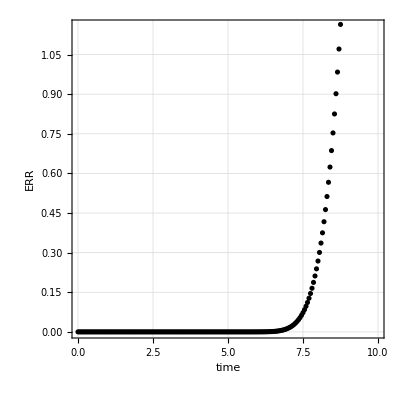
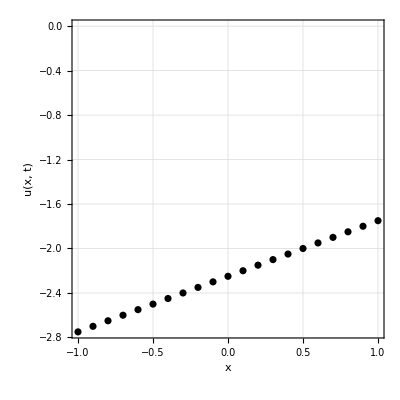
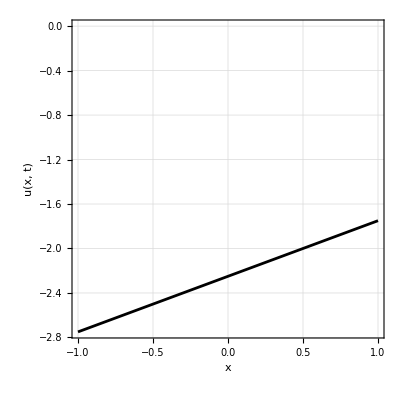

```mathematica
LTEPlotDATAtime[data_, sol_,  time_ :0, ifjoin_: False]:= Module[{plotdata},
coord1 = FindIndex[data[[1]][[2;;]], -1];
coord2 = FindIndex[data[[1]][[2;;]], 1];

plotdata = ListPlot[Table[{data[[1]][[coord]],data[[time]][[coord]]},{coord, coord1,coord2, 1}
], Joined->ifjoin, PlotRange->{{-1, 1},Automatic}, AxesLabel->{"x", "u(x, t)"},
   PlotStyle -> Black, ImageSize->{400,400},LabelStyle->{FontSize->15},
AspectRatio->1, Frame->True,AxesOrigin->{0,0}, GridLines->Automatic(*, PlotLabel->"Численное"*)];
plotdata
]



LTEPlotSOLtime[data_, sol_,  time_:0 , ifjoin_: False]:= Module[{plotsol, coord1, coord2},

coord1 = FindIndex[data[[1]][[2;;]], -1];
coord2 = FindIndex[data[[1]][[2;;]], 1];

plotsol = ListPlot[Table[{data[[1]][[coord]], Evaluate[sol /. {t-> data[[time]][[1]], x -> data[[1]][[coord]]}]}, {coord, coord1,coord2, 1}
], Joined->ifjoin, PlotRange->{{-1, 1},Automatic}, AxesLabel->{"x", "u(x, t)"},   PlotStyle -> Black, ImageSize->{400,400},LabelStyle->{FontSize->15},AspectRatio->1, Frame->True,AxesOrigin->{0,0}, GridLines->Automatic (*, PlotLabel->"Точное"*)];
plotsol
]


LTEPlotERR[data_, sol_,  ifjoin_: False]:= Module[{ploterr,tab, norm, coord1, coord2},
coord1 = FindIndex[data[[1]][[2;;]], -1];
coord2 = FindIndex[data[[1]][[2;;]], 1];

Print["Диапазон: ", {coord1, coord2}];

tab = Table[{data[[time]][[1]],
Sum[Abs[data[[time]][[coord]] - Evaluate[sol/.{x->data[[1]][[coord]], t-> data[[time]][[1]]}]], {coord, coord1,coord2, 1}]},

 {time, 2,Length@data, 1}];
norm = Sum[tab[[i]][[2]], {i, 1, Length@tab}];
Print[norm];


ploterr = ListPlot[tab,
Joined->False, PlotRange->{{0, data[[-1]][[1]]},Automatic}, AxesLabel->{"time", "ERR"},PlotStyle -> Black, ImageSize->{400,400},LabelStyle->{FontSize->15},AspectRatio->1,AxesOrigin->{0,0}, Frame->True, GridLines->Automatic(*, PlotLabel->"Ошибка"*)];
ploterr

]

LTEPlottimeALL[data_, sol_,  time_: 0, ifjoin_: False]:= Module[{ploterr,coord1, coord2},
LTEPlotDATAtime[data, sol,time, ifjoin]
LTEPlotSOLtime[data, sol,time,True]
LTEPlotERR[data, sol,ifjoin]
]
sol = 1/2 (1-t+x);
data1= Import["test1\\test1_LD2e.txt", "Table"];
data2= Import["test1\\test1_LD2i.txt", "Table"];
data3= Import["test1\\test1_LD3e.txt", "Table"];
data4= Import["test1\\test1_LD3i.txt", "Table"];
data5= Import["test1\\test1_Lax.txt", "Table"];
data6= Import["test1\\test1_LaxWen.txt", "Table"];

(*data1= Import["test4\\test4_LD2e.txt", "Table"];
data2= Import["test4\\test4_LD2i.txt", "Table"];
data3= Import["test4\\test4_Lax.txt", "Table"];
data4 = Import["test4\\test4_LaxWen.txt", "Table"];
data5= Import["test4\\test4_LD3e.txt", "Table"];*)
(*data1= Import["test2\\test2_LD2e.txt", "Table"];
data2= Import["test2\\test2_LD2i.txt", "Table"];
data3= Import["test2\\test2_Lax.txt", "Table"];
data4 = Import["test2\\test2_LaxWen.txt", "Table"];
data5= Import["test2\\test2_LD3e.txt", "Table"];*)

(*sol =1/3 (1-Cos[π (1-t+x)]);*)
sol = 1/2 (1-t+x);
LTEPlottimeALL[data5, sol, 112]
```